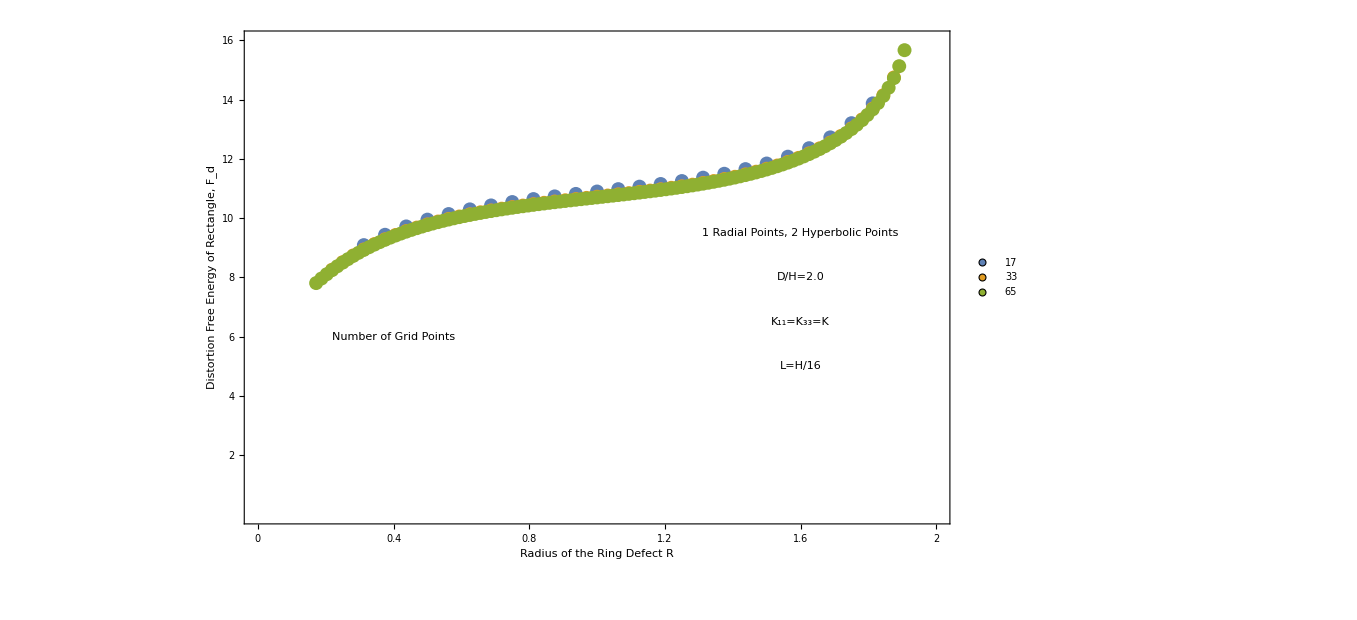

```mathematica
a={{0.312500,9.091297},{0.375000,9.440327},{0.437500,9.722003},{0.500000,9.951466},
{0.562500,10.140450},{0.625000,10.297973},{0.687500,10.431097},{0.750000,10.545495},
{0.812500,10.645865},{0.875000,10.736218},{0.937500,10.820102},{1.000000,10.900772},
{1.062500,10.981346},{1.125000,11.064938},{1.187500,11.154807},{1.250000,11.254509},
{1.312500,11.368089},{1.375000,11.500328},{1.437500,11.657095},{1.500000,11.845882},
{1.562500,12.076701},{1.625000,12.363705},{1.687500,12.728472},{1.750000,13.207706},
{1.812500,13.875794}};

a2={{0.218750,8.259710},{0.250000,8.514684},{0.281250,8.742253},{0.312500,8.945212},
{0.343750,9.126459},{0.375000,9.288696},{0.406250,9.434320},{0.437500,9.565410},
{0.468750,9.683756},{0.500000,9.790902},{0.531250,9.888184},{0.562500,9.976766},
{0.593750,10.057671},{0.625000,10.131803},{0.656250,10.199968},{0.687500,10.262893},
{0.718750,10.321231},{0.750000,10.375583},{0.781250,10.426497},{0.812500,10.474485},
{0.843750,10.520022},{0.875000,10.563556},{0.906250,10.605516},{0.937500,10.646312},
{0.968750,10.686340},{1.000000,10.725991},{1.031250,10.765652},{1.062500,10.805708},
{1.093750,10.846552},{1.125000,10.888585},{1.156250,10.932221},{1.187500,10.977895},
{1.218750,11.026065},{1.250000,11.077218},{1.281250,11.131880},{1.312500,11.190623},
{1.343750,11.254070},{1.375000,11.322915},{1.406250,11.397928},{1.437500,11.479978},
{1.468750,11.570056},{1.500000,11.669301},{1.531250,11.779041},{1.562500,11.900851},
{1.593750,12.036621},{1.625000,12.188670},{1.656250,12.359907},{1.687500,12.554084},
{1.718750,12.776194},{1.750000,13.033177},{1.781250,13.335198},{1.812500,13.698299},
{1.843750,14.150704},{1.875000,14.751857}};

a3={{0.171875,7.810077},{0.187500,7.963415},{0.203125,8.109039},{0.218750,8.247074},
{0.234375,8.377675},{0.250000,8.501082},{0.265625,8.617603},{0.281250,8.727593},
{0.296875,8.831429},{0.312500,8.929489},{0.328125,9.022142},{0.343750,9.109742},
{0.359375,9.192621},{0.375000,9.271090},{0.390625,9.345439},{0.406250,9.415937},
{0.421875,9.482832},{0.437500,9.546354},{0.453125,9.606717},{0.468750,9.664119},
{0.484375,9.718744},{0.500000,9.770762},{0.515625,9.820332},{0.531250,9.867605},
{0.546875,9.912718},{0.562500,9.955802},{0.578125,9.996979},{0.593750,10.036366},
{0.609375,10.074070},{0.625000,10.110194},{0.640625,10.144836},{0.656250,10.178087},
{0.671875,10.210035},{0.687500,10.240763},{0.703125,10.270351},{0.718750,10.298875},
{0.734375,10.326408},{0.750000,10.353019},{0.765625,10.378775},{0.781250,10.403741},
{0.796875,10.427979},{0.812500,10.451549},{0.828125,10.474510},{0.843750,10.496919},
{0.859375,10.518830},{0.875000,10.540297},{0.890625,10.561374},{0.906250,10.582111},
{0.921875,10.602559},{0.937500,10.622769},{0.953125,10.642789},{0.968750,10.662668},
{0.984375,10.682456},{1.000000,10.702200},{1.015625,10.721948},{1.031250,10.741749},
{1.046875,10.761651},{1.062500,10.781702},{1.078125,10.801953},{1.093750,10.822453},
{1.109375,10.843252},{1.125000,10.864402},{1.140625,10.885955},{1.156250,10.907965},
{1.171875,10.930487},{1.187500,10.953577},{1.203125,10.977293},{1.218750,11.001695},
{1.234375,11.026846},{1.250000,11.052811},{1.265625,11.079655},{1.281250,11.107449},
{1.296875,11.136266},{1.312500,11.166182},{1.328125,11.197277},{1.343750,11.229635},
{1.359375,11.263346},{1.375000,11.298502},{1.390625,11.335203},{1.406250,11.373554},
{1.421875,11.413668},{1.437500,11.455662},{1.453125,11.499665},{1.468750,11.545815},
{1.484375,11.594257},{1.500000,11.645152},{1.515625,11.698671},{1.531250,11.755002},
{1.546875,11.814349},{1.562500,11.876936},{1.578125,11.943011},{1.593750,12.012845},
{1.609375,12.086743},{1.625000,12.165044},{1.640625,12.248131},{1.656250,12.336439},
{1.671875,12.430464},{1.687500,12.530776},{1.703125,12.638043},{1.718750,12.753046},
{1.734375,12.876716},{1.750000,13.010178},{1.765625,13.154810},{1.781250,13.312334},
{1.796875,13.484950},{1.812500,13.675551},{1.828125,13.888068},{1.843750,14.128101},
{1.859375,14.404117},{1.875000,14.730088},{1.890625,15.132312},{1.906250,15.672580}};


ListPlot[{a,a2,a3},PlotStyle->PointSize[0.01], Frame->{True, True, False, False}, FrameTicks->{{{2,4,6,8,10,12,14,16},None},{{0,0.4,0.8,1.2,1.6,2},None}}, PlotRange->{{0,2},{0,16}},FrameLabel->{{"Distortion Free Energy of Rectangle, F_d", None},{"Radius of the Ring Defect R", None}},PlotStyle->PointSize[0.01],LabelStyle->Large,PlotLegends->Placed[PointLegend[{"17", "33", "65"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Bottom}], Epilog->{Text[Style["1 Radial Points, 2 Hyperbolic Points",Large],{1.6,9.5}],Text[Style["D/H=2.0",Large],{1.6,8}],Text[Style["K_11=K_33=K",Large],{1.6,6.5}],Text[Style["L=H/16",Large],{1.6,5}],Text[Style["Number of Grid Points",Large],{0.4,6}]}]
```

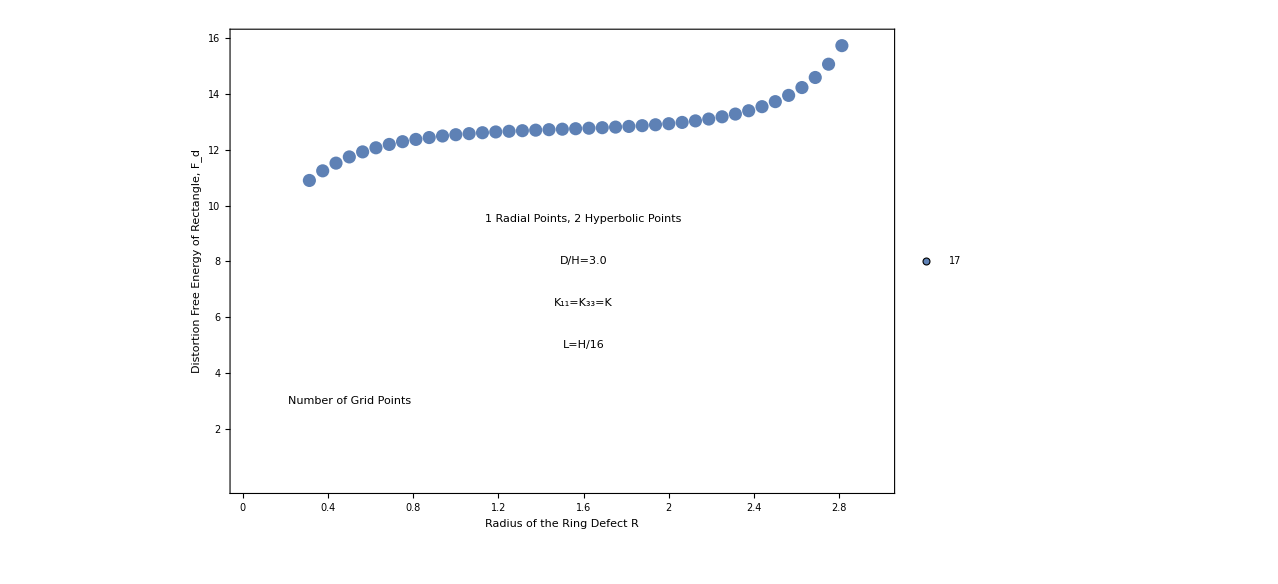

```mathematica
b={{0.312500,10.898921},{0.375000,11.243573},{0.437500,11.519701},{0.500000,11.742238},{0.562500,11.922655},{0.625000,12.069651},{0.687500,12.189890},{0.750000,12.288559},{0.812500,12.369763},{0.875000,12.436789},{0.937500,12.492297},{1.000000,12.538462},{1.062500,12.577073},{1.125000,12.609616},{1.187500,12.637340},{1.250000,12.661300},{1.312500,12.682410},{1.375000,12.701470},{1.437500,12.719202},{1.500000,12.736278},{1.562500,12.753342},{1.625000,12.771039},{1.687500,12.790036},{1.750000,12.811050},{1.812500,12.834875},{1.875000,12.862412},{1.937500,12.894705},{2.000000,12.932986},{2.062500,12.978721},{2.125000,13.033684},{2.187500,13.100033},{2.250000,13.180425},{2.312500,13.278169},{2.375000,13.397442},{2.437500,13.543620},{2.500000,13.723795},{2.562500,13.947651},{2.625000,14.229076},{2.687500,14.589438},{2.750000,15.065273},{2.812500,15.730839}};
ListPlot[{b},PlotStyle->PointSize[0.01], Frame->{True, True, False, False}, FrameTicks->{{{2,4,6,8,10,12,14,16},None},{{0,0.4,0.8,1.2,1.6,2,2.4,2.8,3.2},None}}, PlotRange->{{0,3},{0,16}},FrameLabel->{{"Distortion Free Energy of Rectangle, F_d", None},{"Radius of the Ring Defect R", None}},PlotStyle->PointSize[0.01],LabelStyle->Large,PlotLegends->Placed[PointLegend[{"17"},LegendMarkers->{{Graphics[Disk[]],12}}],{Left, Bottom}], Epilog->{Text[Style["1 Radial Points, 2 Hyperbolic Points",Large],{1.6,9.5}],Text[Style["D/H=3.0",Large],{1.6,8}],Text[Style["K_11=K_33=K",Large],{1.6,6.5}],Text[Style["L=H/16",Large],{1.6,5}],Text[Style["Number of Grid Points",Large],{0.5,3}]}]
```

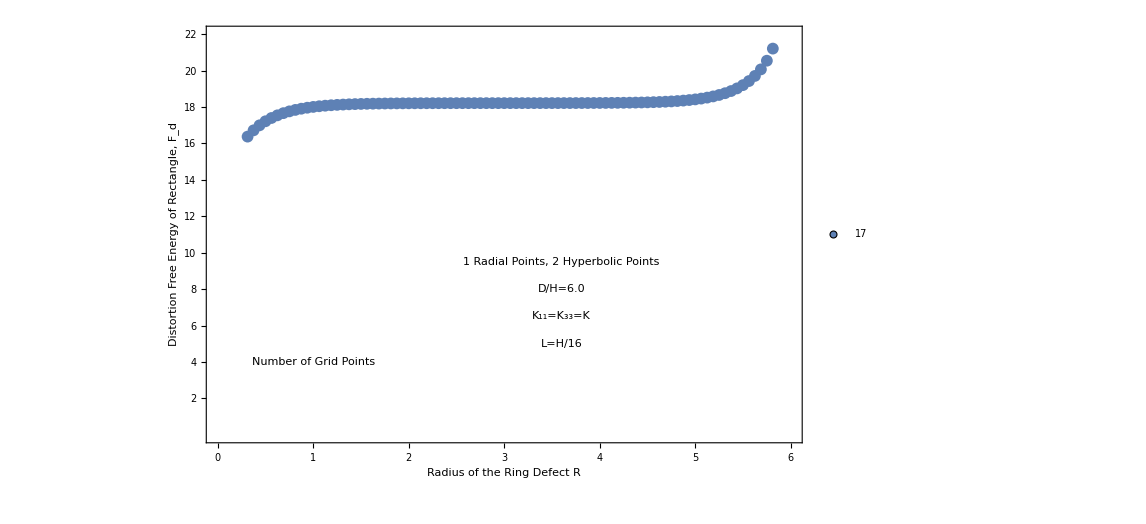

```mathematica
b2={{0.312500,16.375692},{0.375000,16.720137},{0.437500,16.996003},{0.500000,17.218213},{0.562500,17.398226},{0.625000,17.544725},{0.687500,17.664354},{0.750000,17.762280},{0.812500,17.842579},{0.875000,17.908502},{0.937500,17.962671},{1.000000,18.007207},{1.062500,18.043839},{1.125000,18.073979},{1.187500,18.098784},{1.250000,18.119202},{1.312500,18.136010},{1.375000,18.149849},{1.437500,18.161243},{1.500000,18.170626},{1.562500,18.178352},{1.625000,18.184715},{1.687500,18.189956},{1.750000,18.194272},{1.812500,18.197828},{1.875000,18.200757},{1.937500,18.203170},{2.000000,18.205159},{2.062500,18.206798},{2.125000,18.208150},{2.187500,18.209265},{2.250000,18.210186},{2.312500,18.210947},{2.375000,18.211577},{2.437500,18.212101},{2.500000,18.212537},{2.562500,18.212902},{2.625000,18.213210},{2.687500,18.213473},{2.750000,18.213701},{2.812500,18.213901},{2.875000,18.214082},{2.937500,18.214251},{3.000000,18.214413},{3.062500,18.214576},{3.125000,18.214744},{3.187500,18.214925},{3.250000,18.215126},{3.312500,18.215353},{3.375000,18.215616},{3.437500,18.215924},{3.500000,18.216289},{3.562500,18.216725},{3.625000,18.217248},{3.687500,18.217878},{3.750000,18.218639},{3.812500,18.219559},{3.875000,18.220673},{3.937500,18.222024},{4.000000,18.223661},{4.062500,18.225647},{4.125000,18.228056},{4.187500,18.230979},{4.250000,18.234526},{4.312500,18.238831},{4.375000,18.244056},{4.437500,18.250398},{4.500000,18.258094},{4.562500,18.267434},{4.625000,18.278771},{4.687500,18.292531},{4.750000,18.309233},{4.812500,18.329507},{4.875000,18.354120},{4.937500,18.384006},{5.000000,18.420304},{5.062500,18.464409},{5.125000,18.518030},{5.187500,18.583276},{5.250000,18.662762},{5.312500,18.759761},{5.375000,18.878425},{5.437500,19.024106},{5.500000,19.203876},{5.562500,19.427404},{5.625000,19.708567},{5.687500,20.068721},{5.750000,20.544397},{5.812500,21.209844}};
ListPlot[{b2},PlotStyle->PointSize[0.01], Frame->{True, True, False, False}, FrameTicks->{{{2,4,6,8,10,12,14,16,18,20,22},None},{{0,1,2,3,4,5,6},None}}, PlotRange->{{0,6},{0,22}},FrameLabel->{{"Distortion Free Energy of Rectangle, F_d", None},{"Radius of the Ring Defect R", None}},PlotStyle->PointSize[0.01],LabelStyle->Large,PlotLegends->Placed[PointLegend[{"17"},LegendMarkers->{{Graphics[Disk[]],12}}],{Left, Bottom}], Epilog->{Text[Style["1 Radial Points, 2 Hyperbolic Points",Large],{3.6,9.5}],Text[Style["D/H=6.0",Large],{3.6,8}],Text[Style["K_11=K_33=K",Large],{3.6,6.5}],Text[Style["L=H/16",Large],{3.6,5}],Text[Style["Number of Grid Points",Large],{1,4}]}]
```

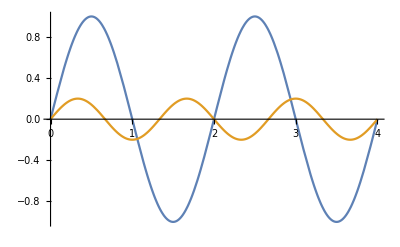

```mathematica
Plot[{Sin[π×x],0.2×Sin[(3×π×x)/2]},{x,0,4}]
```

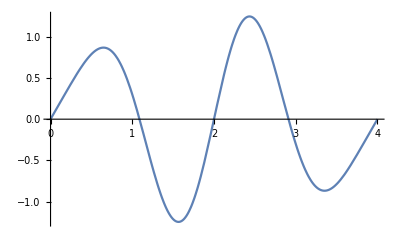

```mathematica
Plot[{Sin[π×x]-0.3×Sin[(3×π×x)/2]},{x,0,4}]
```